## Aqui estão minhas funções validadas para passar ao outro arquivo

## Daqui para abaixo população para testes

fazer os testes de Limites, todo mundo empregado, todo mundo desempregado, todo mundo na classe mais alta ou em uma classe só, e todo mundo na classe mais baixa =)
verificar os resultados se são esperados e se não da erro

funções que faltam
Atualizar status População - restrito

```mathematica
empregadorR[populacao_List, desemprego_,qtr_]:= ( pop = empregado[populacao];
                                                                                                                des = 0;
												res = 0;	
				                                                                       While[des≤desempregado,
												in = RandomInteger[{1,Length[populacao]}];
												
										
                                                                                                                                          atribuirDE[pop[[in]],"D"];                                                                                           
									
											       des = contar[contDes[pop]]
                                                                                                           ];
												pop				
												);
```

```mathematica
verER[familia_List]:= If[familia[[2]] =="E" && familia[[3]] ≠ "A", atribuirDE[familia,"D" ],familia];
verE[familia_List]:= If[familia[[2]] =="E", atribuirDE[familia,"D" ],familia ]
```

```mathematica
contDes[populacao_List]:= Prepend[contDes[Rest[populacao]], contD[First[populacao]]];
contDes[{}]:= {};
contD[{}]:= {};
contD[familia_List]:= If[familia[[2]] == "D",1,0];
```

```mathematica
tst2 = empregadorR[tst,30,2]
```

empregadorR[tst,30,2]

```mathematica
contar[contDes[tst2]]
```

contar[contDes[empregadorR[tst,30,2]]]

```mathematica
0

verER[tst2[[1]]]
```

0

verER[tst]

```mathematica
If[res≤ qtr,verE[pop[[in]]],
                                                                                                                                          verER[pop[[in]]]];                                                                                           

												If[pop[[in,2]]=="D" && pop[[in,3]]=="A",res++];	
											       des = contar[contDes[pop]]
                                                                                                           ];
```

```mathematica
simular[iter_Integer,tamanho_Integer]:= ( pop = populacaoAl[tamanho];
ie = {0.0034,0.007,0.07,0.15,0.2};
ptrc = confPTRC[30,200,50,150];
tbr = tblIR[1787.77,2679.29,3572.43,4463.81,7.5,15,22.5,.275];
retornoIE = 1.28;
salarioM = 100;
divClass = {0.5,2,11,20};
gov = iniGov[iter];
gov = iniGov[iter];
controlep = controlPop[iter];
For[i=0, i≤ iter,i++,
	pop = empregador[pop,30]; 	
	pop=invEduN[pop,ie,salarioM];
	
	pop = calculoRendaN[pop,salarioM,divClass ,retornoIE,ie,3.3];
	pop = tranferir[pop,3.3,salarioM/2,50,140];
	gov[[i]] =ReplacePart[gov[[i]],{3-> contar[beneficiarios[pop]],
								4-> contar[valorTransfN[pop]],
								2-> arrecadar[arrecadar[pop,tbr]]}];
	controlep[[i]]= ReplacePart[controlep[[i]], { 2 -> contar[classE[pop,"E"]], 3 -> contar[classE[pop,"D"]],
                                                                            4-> contar[classE[pop,"C"]],5-> contar[classE[pop,"B"]], 
                                                                           6-> contar[classE[pop,"A"]],7 -> contar[rendaE[pop,"E"]],
                                                                           8-> contar[rendaE[pop,"D"]], 9 -> contar[rendaE[pop,"C"]],
	                                                                 10 -> contar[rendaE[pop,"B"]], 11 -> contar[rendaE[pop,"A"]]}];         

	pop = alteraClasseN[pop,divClass,salarioM]; 
	pop = mortePop[pop, 78]
     
]

(*salvar os valores do gov e da pop em algum lugar*)
);
```

```mathematica
Essa é função que estiu trabahando
```

```mathematica
simular[10,10,con,invE, 1.25,divClass,4,10]
```

Execução da simulação do projeto

```mathematica
con = {4.16,4.15,38.62,26.26};
ie= {0.0034,0.007,0.07,0.15,0.2};
saldivClass= {1.75,2.75,12,15.55};
tamanho = 500;
iter = 166;
iniPTRC = 11;
fimPTRC = 166;
retIE = 1.47;

desemprego= {12.9,12.5,11.9,11.6,11.9,11.7,11.5,11.2,10.9,10.5,11.2,11.6,12.1,12.4,12.9,13,12.8,13,13,12.9,12.2,10.9,11.7,12,12.8,13.1,12.2,11.7,11.2,11.4,10.9,10.5,10.7,9.6,10.2,10.7,10.8,10.8,10.2,9.4,9.4,9.4,9.6,9.6,9.6,8.4,9.3,10.1,10.4,10.4,10.2,10.4,10.7,10.6,10,9.8,9.5,8.4,9.3,9.9,10.2,10.2,10.2,9.7,9.5,9.5,9,8.7,8.2,7.4,8,8.7,8.6,8.5,7.9,7.8,8.1,7.6,7.7,7.5,7.6,6.8,8.2,8.5,9,8.9,8.8,8.1,8,8.1,7.7,7.5,7.3,6.8,7.2,7.4,7.6,7.3,7.4,7,6.9,6.7,6.2,6,5.7,5.3,6,6.3,6.4,6.4,6.3,6.2,6,6,6,5.7,5.2,4.7,5.5,5.7,6.2,6,5.8,5.9,5.4,5.3,5.4,5.3,4.9,4.6,5.5,5.6,5.7,5.8,5.8,6,5.6,5.3,5.4,5.2,4.6,4.3,4.8,5.1,5,4.8,4.9,4.8,4.9,5,4.8,4.6,4.8,4.3,5.3,5.8,6.1,6.4,6.7,6.9,7.5,7.5,7.5,7.8,7.5,6.9};
salarioMin = {180,200,200,200,200,200,200,200,200,200,200,200,200,240,240,240,240,240,240,240,240,240,240,240,240,240,260,260,260,260,260,260,260,260,260,260,260,260,300,300,300,300,300,300,300,300,300,300,300,300,350,350,350,350,350,350,350,350,350,350,350,380,380,380,380,380,380,380,380,380,380,380,415,415,415,415,415,415,415,415,415,415,415,465,465,465,465,465,465,465,465,465,465,465,510,510,510,510,510,510,510,510,510,510,510,510,540,540,545,545,545,545,545,545,545,545,545,545,622,622,622,622,622,622,622,622,622,622,622,622,678,678,678,678,678,678,678,678,678,678,678,678,724,724,724,724,724,724,724,724,724,724,724,724,788,788,788,788,788,788,788,788,788,788,788,788};
```

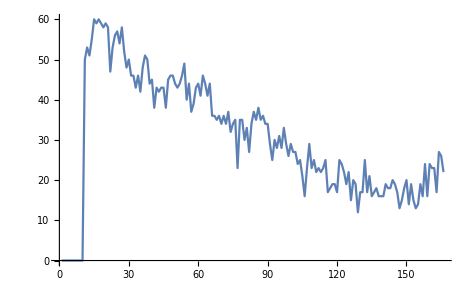
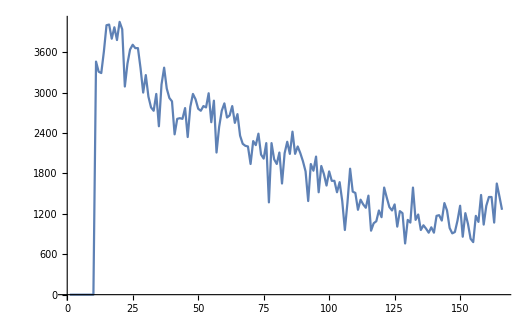
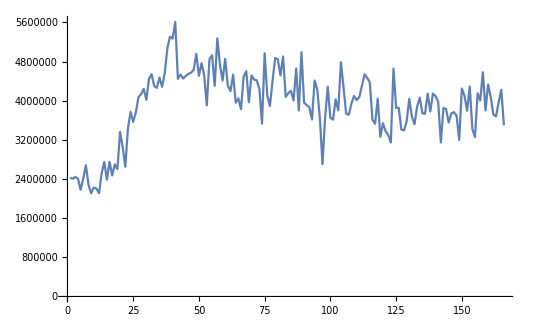
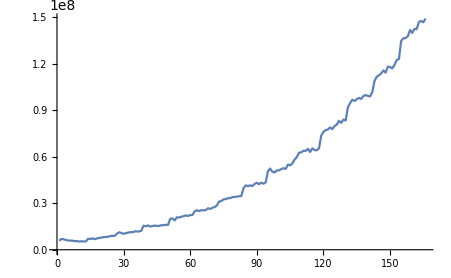
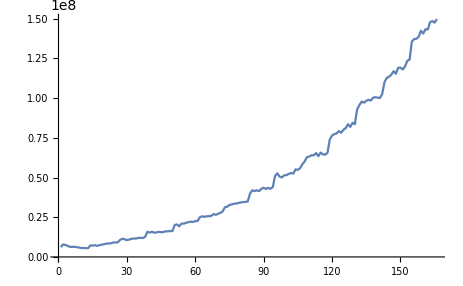
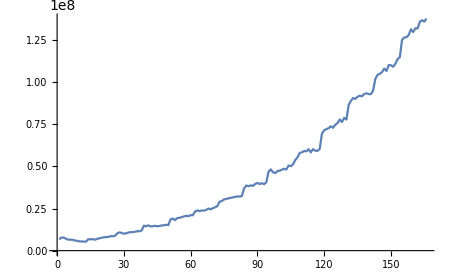
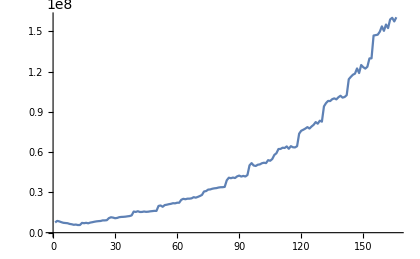
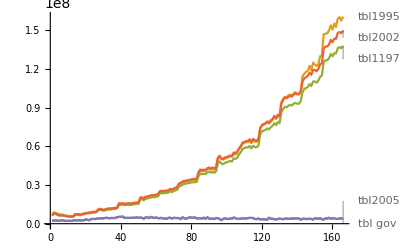
Null -Graphics- -Graphics- -Graphics- -Graphics- -Graphics- -Graphics- -Graphics- -Graphics- -Graphics-

```mathematica
ProjetoIR[iter,tamanho,con,ie,retIE,saldivClass,iniPTRC,fimPTRC,salarioMin,desemprego]
```

```mathematica
pop
```